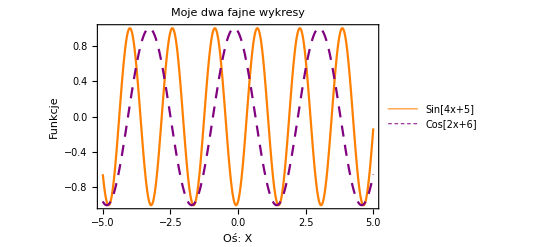

```mathematica
(*Sin(4x+5) oraz Cos(2x+6)*)
(*Uwaga: dodatkowo opisz dokładnie wykres wraz z legendą*)
Plot[{Sin[4x+5],Cos[2*x-6]},{x,-5,5},Frame->True,FrameLabel->{StyleForm["Oś: X",FontSize->14,Black],StyleForm["Funkcje",FontSize->14,Red]},PlotStyle->{{Thickness[0.004],Orange},{Thickness[0.004],Dashing[{0.02,0.015}],Purple}},PlotLegends->{"Sin[4x+5]","Cos[2x+6]"},BaseStyle->{FontFamily->Times,FontSize->14},ImageSize->Scaled[0.7],PlotLabel->StyleForm["Moje dwa fajne wykresy",FontSize->14,Green]]
```

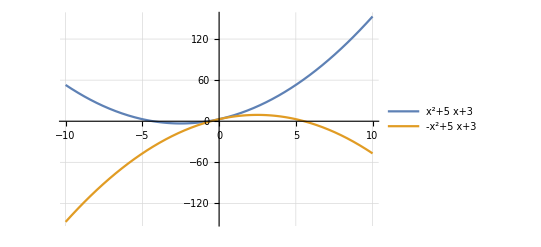

```mathematica
(*Grid, Siatka szablon*)
Plot[{x^2+5 x+3,-x^2+5 x+3},{x,-10,10},GridLines->Automatic,PlotLegends->"Expressions"]
```

3+5 x+x^2

3+5 x-x^2

3+5 x+x^2

3+5 x-x^2

3+5 x+x^2

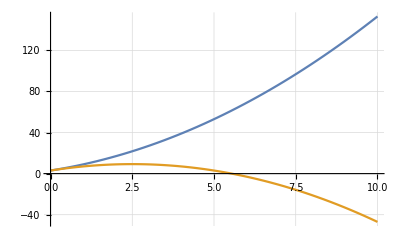

```mathematica
Grid[{{w1},{},{w2}}]
Grid[{{w1},{},{w2},{},{w1}}]

Plot[{w1,w2},{x,0,10},GridLines->Automatic]
```